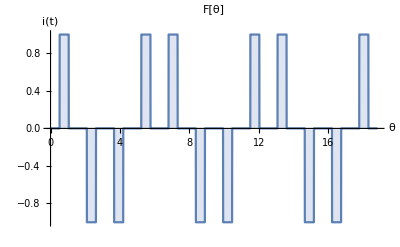

```mathematica
Clear["Global`*"]
(*Función*)
T= 2π; (*Periodo Angular*)
Ttemporal =T/50;
ϕ = π/6;
duty = 1/2;
(*F[θ_] := 2*UnitBox[Mod[variable/T,1.]/(2. duty)]-1*)
Faux[θ_] := UnitStep[θ-π/6]- UnitStep[θ - (2π/6)]- UnitStep[θ-(4π/6)]+UnitStep[θ-((5π)/6)] -UnitStep[θ-((7π)/6)] + UnitStep[θ-((8π)/6)] + UnitStep[θ-((10π)/6)] - UnitStep[θ-((11π)/6)]
F[θ_]:= Faux[Mod[θ,T,0]];
Plot[{F[θ]},{θ,0,3T}, PlotLabel->"F[θ]",AxesLabel->{"θ","i(t)"},Filling->Axis]
```

```mathematica
(*Gráfico de la función*)
```

Valor RMS de F[θ]: 0.57735

Valor RMS del Armonico h: (8 √2 √(((1+2 Cos[(h π)/6])^4 Cos[(h π)/4]^2 Sin[(h π)/12]^6)/h^2))/π

Valor RMS de la fundamental 0.329539

Corriente de distorsión: -(2 (-1+√3) Cos[t])/π-UnitStep[-(11 π)/6+Mod[50 t,2 π,0]]+UnitStep[-(5 π)/3+Mod[50 t,2 π,0]]+UnitStep[-(4 π)/3+Mod[50 t,2 π,0]]-UnitStep[-(7 π)/6+Mod[50 t,2 π,0]]+UnitStep[-(5 π)/6+Mod[50 t,2 π,0]]-UnitStep[-(2 π)/3+Mod[50 t,2 π,0]]-UnitStep[-π/3+Mod[50 t,2 π,0]]+UnitStep[-π/6+Mod[50 t,2 π,0]]

Valor RMS de la corriente de distorsión: 0.474065

THD: 143.857

Factor de potencia: 0.494308

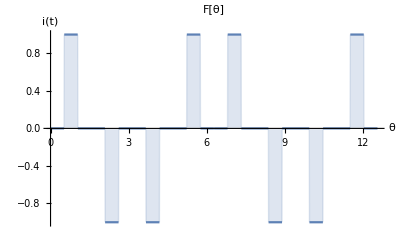

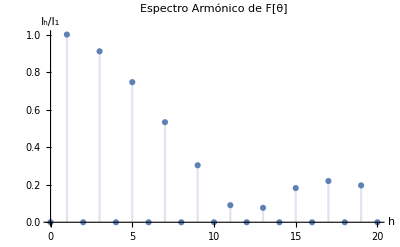

```mathematica
(*Análisis Armónico*)
RMSF = √(1/T∫_(-T/2)^(T/2) F[θ]^2 ⅆθ);
ah[h_]:= 2/T∫_(-T/2)^(T/2) (F[θ]*Cos[h*θ])ⅆθ
bh[h_]:=2/T∫_(-T/2)^(T/2) (F[θ]*Sin[h*θ])ⅆθ
serieFourier[θ_,n_]:= 1/2∫_(-T/2)^(T/2) F[θ]ⅆθ + ∑_(h=1)^n (ah[h]*Cos[h*θ] + bh[h]*Sin[h*θ]);
RMSh[h_]:=(√(ah[h]^2+bh[h]^2))/(√2);
iDis = F[(2π)/Ttemporal*t] - FourierSeries[F[t],t,1];
RMSiDis = √(RMSF^2-RMSh[1]^2);
THDi = 100*(RMSiDis/RMSh[1]);
DPF = Cos[π/6];
PF = RMSh[1]/RMSF*Cos[ϕ];
(*Salida datos*)
Print["Valor RMS de F[θ]: ", RMSF//N]
Print["Valor RMS del Armonico h: ", FullSimplify[RMSh[h]]]
Print["Valor RMS de la fundamental ", FullSimplify[RMSh[1]]//N]
Print["Corriente de distorsión: ", FullSimplify[iDis]]
Print["Valor RMS de la corriente de distorsión: ", RMSiDis//N]
Print["THD: ", THDi//N]
Print["Factor de potencia: ", PF//N]

Plot[{F[θ]},{θ,0,4π}, PlotLabel->"F[θ]",AxesLabel->{"θ","i(t)"},Filling->Axis]
DiscretePlot[RMSh[h]/RMSh[1],{h,0,20},PlotLabel->"Espectro Armónico de F[θ]", PlotRange->Full, AxesLabel->{"h","I_h/I_1"}]
(*Plot[iDis,{t, 0,1},PlotRange->All, PlotLabel->"Corriente de distorsión",Filling->Axis]s*)
```

```mathematica
g[h_]:=(8 √2 √(((1+2 Cos[(h π)/6])^4 Cos[(h π)/4]^2 Sin[(h π)/12]^6)/h^2))/π
g[1]
ah[h]
bh[h]
```

((-1+√3)^3 (1+√3)^2)/(2 √2 π)

-(2 (Sin[(h π)/6]-Sin[(h π)/3]-Sin[(2 h π)/3]+Sin[(5 h π)/6]))/(h π)

0